# Front SUS kinematics

-Graphics--Graphics-

```mathematica
ClearAll["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\feder\Desktop\University\FormulaSAE\DMT\Motion capture

## Rotation matrix

Useful functions used in the script

```mathematica
translate = Function[{x,y,z},
({{1, 0, 0, x}, {0, 1, 0, y}, {0, 0, 1, z}, {0, 0, 0, 1}})
];
```

```mathematica
rotate=Function[{axis,θ},
If[axis=="X",R=({{1, 0, 0, 0}, {0, Cos[θ], -Sin[θ], 0}, {0, Sin[θ], Cos[θ], 0}, {0, 0, 0, 1}}),
If[axis=="Y",R=({{Cos[θ], 0, Sin[θ], 0}, {0, 1, 0, 0}, {-Sin[θ], 0, Cos[θ], 0}, {0, 0, 0, 1}}),
If[axis=="Z",R=({{Cos[θ], -Sin[θ], 0, 0}, {Sin[θ], Cos[θ], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}}),0]]];
R];
```

Get the coordinates of the reference frame RF in respect to ground

```mathematica
getPoint=Function[RF,
{RF[[1,4]],RF[[2,4]],RF[[3,4]]}
];
```

```mathematica
makePoint=Function[{RF,x,y,z},
getPoint[RF.translate[x,y,z]]
];
```

```mathematica
invFrame=Function[RF,
rm=Transpose[RF[[1;;3,1;;3]]];
po=-rm.RF[[1;;3,4]];
({{rm[[1,1]], rm[[1,2]], rm[[1,3]], po[[1]]}, {rm[[2,1]], rm[[2,2]], rm[[2,3]], po[[2]]}, {rm[[3,1]], rm[[3,2]], rm[[3,3]], po[[3]]}, {0, 0, 0, 1}})
];
```

Function to get the rotation matrix of a certain transformation matrix

```mathematica
getRotation=Function[RF,
({{RF[[1,1]], RF[[1,2]], RF[[1,3]]}, {RF[[2,1]], RF[[2,2]], RF[[2,3]]}, {RF[[3,1]], RF[[3,2]], RF[[3,3]]}})
];
```

```mathematica
intersection=Function[{P1,P2,P3,P4},
solution=Solve[{
y==(P2[[2]]-P1[[2]])/(P2[[1]]-P1[[1]])*x+P1[[2]]-(P2[[2]]-P1[[2]])/(P2[[1]]-P1[[1]])*P1[[1]],
y==(P4[[2]]-P3[[2]])/(P4[[1]]-P3[[1]])*x+P3[[2]]-(P4[[2]]-P3[[2]])/(P4[[1]]-P3[[1]])*P3[[1]]
},{x,y}];
res={x,y}/.solution[[1]]
];
```

## Data

Importing vehicle data and suspension points

```mathematica
Data =Import["VehicleData.json","RawJson"];
VehicleData=Normal[Data]/.(k_String->v_):>(Symbol[k]->v)
```

{g→9.81,rhoair→1.225,wr→1.21,wf→1.27,Lr→0.827,L→1.53,m→284,Lf→0.703,mDriver→70,rr→0.203,rf→0.203,lx→0.3,ly→0.3,mur→7.8,muf→7.2,Ixx→27.96,Iyy→89.74,Izz→96.13,Ixz→7.5,Iwar→0.094,Iwaf→0.079,gammarr0→-0.0087,gammarl0→-0.0087,gammafr0→-0.0436,gammafl0→-0.0436,kB→0.6,Tbmax→750,hG→0.3,deltarr0→0.0044,deltarl0→0.0044,deltafr0→-0.0061,deltafl0→-0.0061}

```mathematica
Data2=Import["FrontSuspensionPoints.json","RawJson"];
dataKine=Normal[Data2]/.(k_String->v_):>(Symbol[k]->v)
```

{x1→1.39402,x2→1.7266,x3→1.3975,x4→1.7231,x9→1.53,x12→1.50239,y1→0.225388,y2→0.185,y3→0.282,y4→0.225,y9→0.62,y12→0.13,z1→0.145957,z2→0.123904,z3→0.265031,z4→0.25041,z9→0.2032,z12→0.606931,x6→-0.0276075,x7→-0.00697972,x10→-0.0276075,xC→0,y6→-0.0556075,y7→-0.0349797,y10→-0.081535,yC→0,z6→0.0868,z7→-0.0812,z10→0.096911,zC→-0.2032,x8→-0.095,y8→-0.058,z8→-0.0378688,x5→1.5,y5→0.223606,z5→0.163,rPinion→0.018}

Choose kinematic intervals to study (vertical chassis motion and roll angle)

```mathematica
nsteps=21;
(*Vertical chassis motion*)
ΔZmin=-0.06;
ΔZmax=0.06;
(*Roll angle*)
ϕmin=-4*π/180;
ϕmax=4*π/180;
(*Steering angle*)
δmin=-110*π/180;
δmax=110*π/180;
```

### Setup

- Static camber -- γ0
- Static toe -- δ0

```mathematica
setup={γ0->0,δ0->0,ΔZ0->0};
```

Import the ideal solution and the kinematic intervals for the numeric solution
This variables represent the movement and rotation of the hub+wheel

```mathematica
solKineIdeal={xWl[t]->0,xWr[t]->0,yWl[t]->0,yWr[t]->0,zWl[t]->0,zWr[t]->0,γWl[t]->0,γWr[t]->0,θWl[t]->0,θWr[t]->0,δWl[t]->0,δWr[t]->0};
```

```mathematica
intervals={-0.1<=xWr[t]<=0.1,-0.1<=yWr[t]<=0.1,-0.1<=zWr[t]<=0.1,-Pi/2<=δWr[t]<=Pi/2,-Pi/2<=γWr[t]<=Pi/2,-Pi/2<=θWr[t]<=Pi/2,-0.1<=xWl[t]<=0.1,-0.1<=yWl[t]<=0.1,-0.1<=zWl[t]<=0.1,-Pi/2<=δWl[t]<=Pi/2,-Pi/2<=γWl[t]<=Pi/2,-Pi/2<=θWl[t]<=Pi/2};
```

## Kinematics analysis

### Kinematic definitions

Ground (road surface)

```mathematica
RF0=IdentityMatrix[4];
```

#### Hub + wheel

Hub + Wheel reference frame (static configuration + hub motion)

```mathematica
RFhl=translate[x9+xWl[t],y9+yWl[t],z9+zWl[t]].rotate["Z",δ0+δWl[t]].rotate["X",-γ0+γWl[t]].rotate["Y",θWl[t]];
RFhr=translate[x9+xWr[t],-y9+yWr[t],z9+zWr[t]].rotate["Z",δ0+δWr[t]].rotate["X",-γ0+γWr[t]].rotate["Y",θWr[t]];
```

Points defined in the hub bracket reference frame

```mathematica
P9l=getPoint[RFhl]; (*Wheel center*)
PCl=makePoint[RFhl,xC,yC,zC];(*Contact point with ground*)
P6l=makePoint[RFhl,x6,y6,z6];(*Upper outboard attatchment point*)
P7l=makePoint[RFhl,x7,y7,z7];(*Lower outboard attatchment point*)
P8l=makePoint[RFhl,x8,y8,z8];(*Outboard tie rod attatchment point*)

P9r=getPoint[RFhr];
PCr=makePoint[RFhr,xC,-yC,zC];
P6r=makePoint[RFhr,x6,-y6,z6];
P7r=makePoint[RFhr,x7,-y7,z7];
P8r=makePoint[RFhr,x8,-y8,z8];
```

Degrees of freedom of the hub

```mathematica
dofHub={xWl[t],yWl[t],zWl[t],γWl[t],θWl[t],δWl[t],xWr[t],yWr[t],zWr[t],γWr[t],θWr[t],δWr[t]};
```

#### Chassis

Relative difference between chassis and wheel height -- ΔZ[t]
Roll angle -- ϕ[t]

Chassis reference frame

```mathematica
RFc=RF0.translate[0,0,ΔZ0+ΔZ[t]].rotate["X",ϕ[t]];
```

Points defined in the chassis reference frame

```mathematica
(*four inboard pickup points*)
P1l=makePoint[RFc,x1,y1,z1];
P2l=makePoint[RFc,x2,y2,z2];
P3l=makePoint[RFc,x3,y3,z3];
P4l=makePoint[RFc,x4,y4,z4];
P5l=makePoint[RFc,x5,y5-δDriver[t]*rPinion,z5];
```

```mathematica
P1r=makePoint[RFc,x1,-y1,z1];
P2r=makePoint[RFc,x2,-y2,z2];
P3r=makePoint[RFc,x3,-y3,z3];
P4r=makePoint[RFc,x4,-y4,z4];
P5r=makePoint[RFc,x5,-y5-δDriver[t]*rPinion,z5];
```

Degrees of freedom of the chassis (heave and steering angle)

```mathematica
dofChassis={ΔZ[t],δDriver[t],ϕ[t]};
```

### Degrees of freedom

List of the variables

```mathematica
qVars=Flatten[{dofHub,dofChassis}]
nVars=Length[qVars]
```

{xWl[t],yWl[t],zWl[t],γWl[t],θWl[t],δWl[t],xWr[t],yWr[t],zWr[t],γWr[t],θWr[t],δWr[t],ΔZ[t],δDriver[t],ϕ[t]}

15

Independent coordinate (Degree of freedom)

```mathematica
qI=dofChassis
nI=Length[qI]
```

{ΔZ[t],δDriver[t],ϕ[t]}

3

Dependent coordinates

```mathematica
qD=Complement[qVars,qI]
nD=Length[qD]
```

{xWl[t],xWr[t],yWl[t],yWr[t],zWl[t],zWr[t],γWl[t],γWr[t],δWl[t],δWr[t],θWl[t],θWr[t]}

12

```mathematica
dof0=Thread[qI->0]
```

{ΔZ[t]→0,δDriver[t]→0,ϕ[t]→0}

### Initial configuration

Initial configuration

```mathematica
initConf=Flatten[{dof0,solKineIdeal,setup}]
```

{ΔZ[t]→0,δDriver[t]→0,ϕ[t]→0,xWl[t]→0,xWr[t]→0,yWl[t]→0,yWr[t]→0,zWl[t]→0,zWr[t]→0,γWl[t]→0,γWr[t]→0,θWl[t]→0,θWr[t]→0,δWl[t]→0,δWr[t]→0,γ0→0,δ0→0,ΔZ0→0}

Points in the initial configuration

```mathematica
{P1l0,P2l0,P3l0,P4l0,P5l0,P6l0,P7l0,P8l0,P9l0,P10l0,PCl0}={P1l,P2l,P3l,P4l,P5l,P6l,P7l,P8l,P9l,P10l,PCl}/.initConf;
```

```mathematica
{P1r0,P2r0,P3r0,P4r0,P5r0,P6r0,P7r0,P8r0,P9r0,P10r0,PCr0}={P1r,P2r,P3r,P4r,P5r,P6r,P7r,P8r,P9r,P10r,PCr}/.initConf;
```

### Link length

Rod joint points 6-3

```mathematica
L63l=Norm[P6l0-P3l0];
L63r=Norm[P6r0-P3r0];
```

Rod joint points 6-4

```mathematica
L64l=Norm[P6l0-P4l0];
L64r=Norm[P6r0-P4r0];
```

Rod joint points 8-5

```mathematica
L85l=Norm[P8l0-P5l0];
L85r=Norm[P8r0-P5r0];
```

Rod joint points 7-1

```mathematica
L71l=Norm[P7l0-P1l0];
L71r=Norm[P7r0-P1r0];
```

Rod joint points 7-2

```mathematica
L72l=Norm[P7l0-P2l0];
L72r=Norm[P7r0-P2r0];
```

### Contraints

The constraint equations have the goal of keeping the length of all the links constant

Rod joint points 6-3

```mathematica
Phi2l=Dot[P6l-P3l,P6l-P3l]-L63l^2;
Phi2r=Dot[P6r-P3r,P6r-P3r]-L63r^2;
```

Rod joint points 6-4

```mathematica
Phi3l=Dot[P6l-P4l,P6l-P4l]-L64l^2;
Phi3r=Dot[P6r-P4r,P6r-P4r]-L64r^2;
```

Rod joint points 8-5

```mathematica
Phi4l=Dot[P8l-P5l,P8l-P5l]-L85l^2;
Phi4r=Dot[P8r-P5r,P8r-P5r]-L85r^2;
```

Rod joint points 7-1

```mathematica
Phi5l=Dot[P7l-P1l,P7l-P1l]-L71l^2;
Phi5r=Dot[P7r-P1r,P7r-P1r]-L71r^2;
```

Rod joint points 7-2

```mathematica
Phi6l=Dot[P7l-P2l,P7l-P2l]-L72l^2;
Phi6r=Dot[P7r-P2r,P7r-P2r]-L72r^2;
```

Contact point

```mathematica
Phi8l=PCl[[3]];
Phi8r=PCr[[3]];
```

Full set of constraint equations

```mathematica
Phil={Phi2l,Phi3l,Phi4l,Phi5l,Phi6l,Phi8l};
Phir={Phi2r,Phi3r,Phi4r,Phi5r,Phi6r,Phi8r};
```

Complete set of contraint equations

```mathematica
Phi=Flatten[{Phil,Phir}];
Length[Phi]
```

12

### Kinematic solution

Number of degrees of freedom

```mathematica
nq=Length[qVars]
nc=Length[Phi]
nDof=nq-nc
```

15

12

3

Check

```mathematica
nVars==nc+nI
```

True

## 3D Animation

Wheel points

```mathematica
T=0.1905;(*Tyre thickness*)
Pw1l=getPoint[RFhl.translate[0,T/2,0]];
Pw2l=getPoint[RFhl.translate[0,-T/2,0]];
Pw1r=getPoint[RFhr.translate[0,T/2,0]];
Pw2r=getPoint[RFhr.translate[0,-T/2,0]];
```

```mathematica
guess=Table[{qD[[i]],0},{i,1,nD}];
```

```mathematica
Manipulate[
Graphics3D[{
(*Solving the system*)
eqns=Phi/.setup/.dataKine/.ΔZ[t]->dZ/.ϕ[t]->fi/.δDriver[t]->δ;
sol=FindRoot[eqns,guess];
(*Chassis points*)
PointSize[Large],Blue,
Point[P1l],Point[P2l],Point[P3l],Point[P4l],
Point[P1r],Point[P2r],Point[P3r],Point[P4r],
(*Suspension points*)
Red,Point[P6l],Point[P7l],Point[P9l],Point[P6r],Point[P7r],Point[P9r],White,Point[PCl],Point[PCr],
(*Steering points*)
Green,Point[P5l],Point[P8l],Point[P5r],Point[P8r],
(*Links*)
Thick,Red,Line[{P1l,P7l}],Line[{P2l,P7l}],Line[{P6l,P7l}],Line[{P3l,P6l}],Line[{P4l,P6l}],
Line[{P1r,P7r}],Line[{P2r,P7r}],Line[{P6r,P7r}],Line[{P3r,P6r}],Line[{P4r,P6r}],
Green,Line[{P5l,P8l}],Line[{P5r,P8r}],Line[{P5l,P5r}],
Opacity[0.5],Blue,Polygon[{P1l,P2l,P4l,P3l}],Polygon[{P1r,P2r,P4r,P3r}],Polygon[{P1l,P1r,P3r,P3l}],
Polygon[{P2l,P2r,P4r,P4l}],White,Polygon[{{2,2,0},{2,-2,0},{-2,-2,0},{-2,2,0}}],
(*Wheels*)
Black,Cylinder[{Pw1l,Pw2l},rf],Cylinder[{Pw1r,Pw2r},rf]
}/.sol/.setup/.dataKine/.VehicleData/.ΔZ[t]->dZ/.ϕ[t]->fi/.δDriver[t]->δ,
PlotRange->{{1,2},{-1,1},{-0.2,0.5}},Axes->True,ImageSize->{700,400}],{{dZ,0},ΔZmin,ΔZmax},{{fi,0},ϕmin*2,ϕmax*2},{{δ,0},δmin,δmax}]
```

ReplaceAll::reps: 
   {setup} is neither a list of replacement rules nor a valid dispatch table
     and so cannot be used for replacing.

ReplaceAll::reps: 
   {dataKine} is neither a list of replacement rules nor a valid dispatch
     table and so cannot be used for replacing.

FindRoot::fdss: 
   Search specification guess should be a list with 1 to 5 elements.

ReplaceAll::reps: 
   {FindRoot[eqns, guess]} is neither a list of replacement rules nor a valid
     dispatch table and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps
     will be suppressed during this calculation.

## Roll center animation

Mean chassis attatchment point

```mathematica
P12l=({P1l[[2]],P1l[[3]]}+{P2l[[2]],P2l[[3]]})/2;
P12r=({P1r[[2]],P1r[[3]]}+{P2r[[2]],P2r[[3]]})/2;
P34l=({P3l[[2]],P3l[[3]]}+{P4l[[2]],P4l[[3]]})/2;
P34r=({P3r[[2]],P3r[[3]]}+{P4r[[2]],P4r[[3]]})/2;
```

```mathematica
Manipulate[
Graphics[{
(*Solving the system*)
guess=Table[{qD[[i]],0},{i,1,nD}];
eqns=Phi/.setup/.dataKine/.ΔZ[t]->dZ/.ϕ[t]->fi/.δDriver[t]->0;
sol=FindRoot[eqns,guess];
(*Calculating the ICR*)
{P6lval,P7lval,P12lval,P34lval,P6rval,P7rval,P12rval,P34rval,PClval,PCrval}={{P6l[[2]],P6l[[3]]},{P7l[[2]],P7l[[3]]},P12l,P34l,{P6r[[2]],P6r[[3]]},{P7r[[2]],P7r[[3]]},P12r,P34r,{PCl[[2]],PCl[[3]]},{PCr[[2]],PCr[[3]]}}/.sol/.setup/.dataKine/.ΔZ[t]->dZ/.ϕ[t]->fi/.δDriver[t]->0;
ICRwl=intersection[P12lval,P7lval,P34lval,P6lval];
ICRwr=intersection[P12rval,P7rval,P34rval,P6rval];
ICRchassis=intersection[ICRwl,PClval,ICRwr,PCrval];
(*Chassis points*)
PointSize[Large],Blue,
Point[P12l],Point[P12r],Point[P34l],Point[P34r],
(*Suspension points*)
Red,Point[P6lval],Point[P7lval],Point[{P9l[[2]],P9l[[3]]}],Point[P6rval],Point[P7rval],Point[{P9r[[2]],P9r[[3]]}],White,Point[PClval],Point[PCrval],
(*ICR*)
Orange,Point[ICRwl],Point[ICRwr],PointSize[Large],Green,Point[ICRchassis],
(*Links*)
Thick,Blue,Line[{P12lval,P12rval}],Line[{P12rval,P34rval}],Line[{P12lval,P34lval}],Line[{P34lval,P34rval}],
Red,Line[{P12lval,P7lval}],Line[{P34lval,P6lval}],Line[{P6lval,P7lval}],
Line[{P12rval,P7rval}],Line[{P34rval,P6rval}],Line[{P6rval,P7rval}],
(*ICR lines*)
Opacity[0.2],Orange,Line[{P12lval,ICRwl}],Line[{P12rval,ICRwr}],Line[{P34lval,ICRwl}],Line[{P34rval,ICRwr}],
Green,Line[{ICRwr,PCrval}],Line[{ICRwl,PClval}],
(*Wheels*)
Black,Rotate[Rectangle[{P9l[[2]]-T/2,P9l[[3]]-rf},{P9l[[2]]+T/2,P9l[[3]]+rf}],γWl[t]],
Rotate[Rectangle[{P9r[[2]]-T/2,P9r[[3]]-rf},{P9r[[2]]+T/2,P9r[[3]]+rf}],γWr[t]]
}/.sol/.setup/.dataKine/.VehicleData/.ΔZ[t]->dZ/.ϕ[t]->fi/.δDriver[t]->0,
PlotRange->{{-1,1},{-0.2,0.5}},Axes->True,ImageSize->{700,400}],{{dZ,0},ΔZmin,ΔZmax},{{fi,0},ϕmin*2,ϕmax*2}]
```

```mathematica
Intersection[{0,0},{1,1},{-1,1},{1,-1}]
```

{}

## Suspension parameters

```mathematica
eqns=Phi/.setup/.dataKine/.ΔZ[t]->0/.ϕ[t]->0/.δDriver[t]->0;
sol=FindRoot[eqns,guess];
nominal=Flatten[{sol,setup,dataKine,ΔZ[t]->0,ϕ[t]->0,δDriver[t]->0}];
{P6lval,P7lval,P12lval,P34lval,P6rval,P7rval,P12rval,P34rval,PClval,PCrval}={{P6l[[2]],P6l[[3]]},{P7l[[2]],P7l[[3]]},P12l,P34l,{P6r[[2]],P6r[[3]]},{P7r[[2]],P7r[[3]]},P12r,P34r,{PCl[[2]],PCl[[3]]},{PCr[[2]],PCr[[3]]}}/.nominal;
```

#### FVSAL

```mathematica
ICRwl=intersection[P12lval,P7lval,P34lval,P6lval];
FVSAL=Abs[ICRwl[[1]]]+PClval[[1]]
```

1.26904

#### SVSAL

```mathematica
ICSide=intersection[{P1l[[1]],P1l[[3]]},{P2l[[1]],P2l[[3]]},{P3l[[1]],P3l[[3]]},{P4l[[1]],P4l[[3]]}]/.nominal;
SVSAL=P9l[[1]]-ICSide[[1]]/.nominal
```

5.70659

```mathematica
Graphics[{Red,Point[{P1l[[1]],P1l[[3]]}],Point[{P2l[[1]],P2l[[3]]}],Point[{P3l[[1]],P3l[[3]]}],Point[{P4l[[1]],P4l[[3]]}],Point[PC],Black,Line[{PC,{P2l[[1]],P2l[[3]]}}],Line[{PC,{P4l[[1]],P4l[[3]]}}]}/.nominal,PlotRange->{{-4.5,2},{-0.2,0.8}},Axes->True,ImageSize->{700,200}]
```

-Graphics-

#### RCH

```mathematica
ICRwl=intersection[P12lval,P7lval,P34lval,P6lval];
ICRwr=intersection[P12rval,P7rval,P34rval,P6rval];
ICRchassis=intersection[ICRwl,PClval,ICRwr,PCrval];
RCH=ICRchassis[[2]]
```

0.0801292

#### Kingpin

```mathematica
Dy=(P7l[[2]]-P6l[[2]])/.nominal;
Dz=(P6l[[3]]-P7l[[3]])/.nominal;
kingpin=ArcTan[Dy/Dz]*180/π
```

7.

#### Caster

```mathematica
Dx=-(P7l[[1]]-P6l[[1]])/.nominal;
Dz=(P7l[[3]]-P6l[[3]])/.nominal;
Caster=ArcTan[Dx/Dz]*180/π
```

7.

#### Scrub radius

```mathematica
P=intersection[{P6l[[2]],P6l[[3]]}/.nominal,{P7l[[2]],P7l[[3]]}/.nominal,{0,0},{1,0}];
Scrub=P9l[[2]]-P[[1]]/.nominal
```

0.02

#### Mechanical trail

```mathematica
P=intersection[{P6l[[1]],P6l[[3]]}/.nominal,{P7l[[1]],P7l[[3]]}/.nominal,{0,0},{1,0}];
Scrub = P[[1]] - P9l[[1]] /. nominal
```

0.008

#### Anti lift

```mathematica
AntiLift=ICSide[[2]]/SVSAL
```

0.0903051

#### Anti dive

```mathematica
percFrontBraking=0.7;
AntiDive=percFrontBraking*(ICSide[[2]]/SVSAL)*(L/hG)/.VehicleData
```

0.322389

## Useful plots

### Evaluation sequences

Sequence of z movements in the permitted range (from ΔzMin to ΔzMax equidistanced)

```mathematica
dofSeqZ=Table[{ΔZ[t]->ΔZmin+(ΔZmax-ΔZmin)/nsteps*i,δDriver[t]->0,ϕ[t]->0},{i,0,nsteps}];
zVec=dofSeqZ[[All,1,2]];
```

Sequence of steering position in the permitted range (from steerMin to steerMax equidistanced)

```mathematica
dofSeqS=Table[{ΔZ[t]->0,δDriver[t]->δmin+(δmax-δmin)/nsteps*i,ϕ[t]->0},{i,0,nsteps}];
sVec=N[dofSeqS[[All,2,2]]];
```

Sequence of roll angles in the permitted range (from ϕMin to ϕMax equidistanced)

```mathematica
dofSeqϕ=Table[{ΔZ[t]->0,δDriver[t]->0,ϕ[t]->ϕmin+(ϕmax-ϕmin)/nsteps*i},{i,0,nsteps}];
ϕVec=N[dofSeqϕ[[All,2,2]]];
```

### Steering curves

#### Data

```mathematica
obtainedMotionSl=ConstantArray[{0,0},nsteps+1];(*left wheel*)
obtainedMotionSr=ConstantArray[{0,0},nsteps+1];(*right wheel*)
obtainedMotionZl=ConstantArray[{0,0},nsteps+1];(*bump steer*)
obtainedMotionZr=ConstantArray[{0,0},nsteps+1];(*bump steer*)
obtainedMotionϕl=ConstantArray[{0,0},nsteps+1];(*roll steer*)
obtainedMotionϕr=ConstantArray[{0,0},nsteps+1];(*roll steer*)
For[i=1,i<=nsteps+1,i++,
(*Steering function*)
eqnsS=Phi/.dofSeqS[[i]]/.setup/.dataKine;
obtainedMotionSl[[i,1]]=dofSeqS[[i,2,2]]*180/π;
obtainedMotionSr[[i,1]]=dofSeqS[[i,2,2]]*180/π;
obtainedMotionSl[[i,2]]=FindRoot[eqnsS,guess][[9,2]]*180/π;
obtainedMotionSr[[i,2]]=FindRoot[eqnsS,guess][[10,2]]*180/π;
(*Bump steer*)
eqnsZ=Phi/.dofSeqZ[[i]]/.setup/.dataKine;
obtainedMotionZl[[i,1]]=dofSeqZ[[i,1,2]];
obtainedMotionZl[[i,2]]=FindRoot[eqnsZ,guess][[9,2]]*180/π;
obtainedMotionZr[[i,1]]=dofSeqZ[[i,1,2]];
obtainedMotionZr[[i,2]]=FindRoot[eqnsZ,guess][[10,2]]*180/π;
(*Roll steer*)
eqnsϕ=Phi/.dofSeqϕ[[i]]/.setup/.dataKine;
obtainedMotionϕl[[i,1]]=dofSeqϕ[[i,3,2]]*180/π;
obtainedMotionϕl[[i,2]]=FindRoot[eqnsϕ,guess][[9,2]]*180/π;
obtainedMotionϕr[[i,1]]=dofSeqϕ[[i,3,2]]*180/π;
obtainedMotionϕr[[i,2]]=FindRoot[eqnsϕ,guess][[10,2]]*180/π;
]
```

#### Ackermann

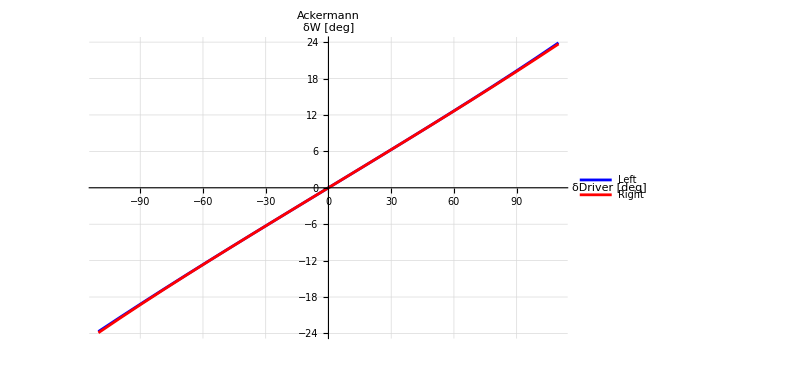

```mathematica
ListPlot[{obtainedMotionSl,obtainedMotionSr},Joined->True,PlotStyle->{Blue,Red},PlotLegends->{"Left","Right"},PlotLabel->Style["Ackermann",FontSize->18],AxesLabel->{"δDriver [deg]","δW [deg]"},GridLines->Automatic,ImageSize->600]
```

#### Bumpsteer

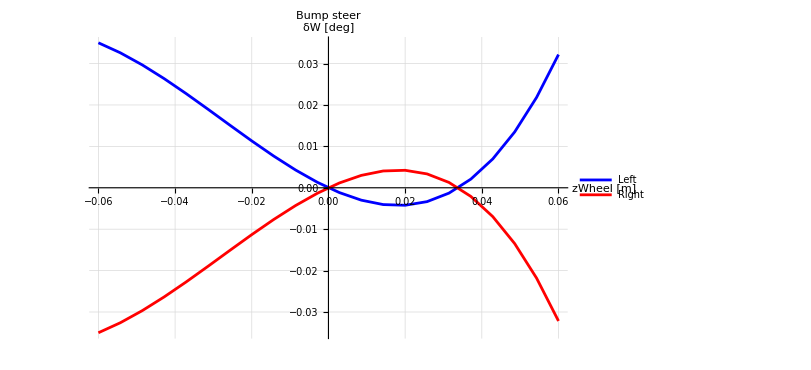

```mathematica
ListPlot[{obtainedMotionZl,obtainedMotionZr},Joined->True,PlotStyle->{Blue,Red},PlotLegends->{"Left","Right"},PlotLabel->Style["Bump steer",FontSize->18],AxesLabel->{"zWheel [m]","δW [deg]"},GridLines->Automatic,ImageSize->600]
```

#### Rollsteer

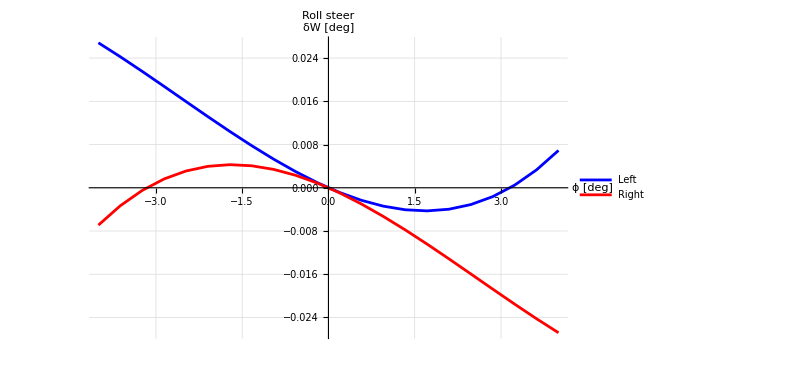

```mathematica
ListPlot[{obtainedMotionϕl,obtainedMotionϕr},Joined->True,PlotStyle->{Blue,Red},PlotLegends->{"Left","Right"},PlotLabel->Style["Roll steer",FontSize->18],AxesLabel->{"ϕ [deg]","δW [deg]"},GridLines->Automatic,ImageSize->600]
```

#### Steering ratio

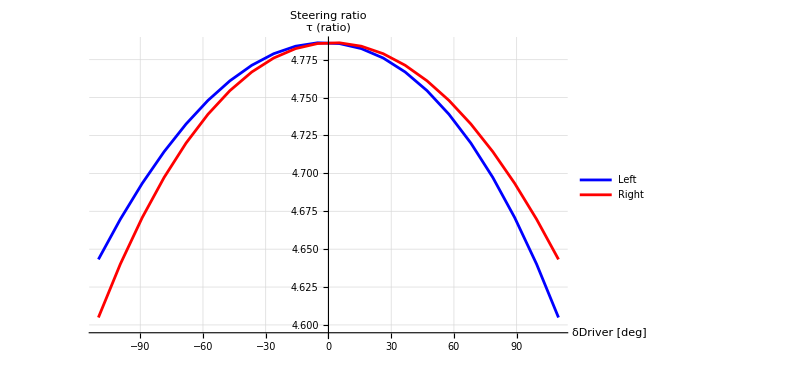

```mathematica
ListPlot[{
Transpose[{obtainedMotionSl[[All,1]],obtainedMotionSl[[All,1]]/obtainedMotionSl[[All,2]]}],Transpose[{obtainedMotionSr[[All,1]],obtainedMotionSr[[All,1]]/obtainedMotionSr[[All,2]]}]},Joined->True,PlotStyle->{Blue,Red},PlotLegends->{"Left","Right"},PlotLabel->Style["Steering ratio",FontSize->18],AxesLabel->{"δDriver [deg]","τ (ratio)"},GridLines->Automatic,ImageSize->600]
```

### Suspension curves

#### Camber gain

```mathematica
obtainedMotionSl=ConstantArray[{0,0},nsteps+1];(*steering*)
obtainedMotionSr=ConstantArray[{0,0},nsteps+1];(*steering*)
obtainedMotionZl=ConstantArray[{0,0},nsteps+1];(*bump*)
obtainedMotionZr=ConstantArray[{0,0},nsteps+1];(*bump*)
obtainedMotionϕl=ConstantArray[{0,0},nsteps+1];(*roll*)
obtainedMotionϕr=ConstantArray[{0,0},nsteps+1];(*roll*)
For[i=1,i<=nsteps+1,i++,
(*camber in steering*)
eqnsS=Phi/.dofSeqS[[i]]/.setup/.dataKine;
obtainedMotionSl[[i,1]]=dofSeqS[[i,2,2]]*180/π;
obtainedMotionSr[[i,1]]=dofSeqS[[i,2,2]]*180/π;
obtainedMotionSl[[i,2]]=FindRoot[eqnsS,guess][[7,2]]*180/π;
obtainedMotionSr[[i,2]]=FindRoot[eqnsS,guess][[8,2]]*180/π;
(*camber in bump*)
eqnsZ=Phi/.dofSeqZ[[i]]/.setup/.dataKine;
obtainedMotionZl[[i,1]]=dofSeqZ[[i,1,2]];
obtainedMotionZl[[i,2]]=FindRoot[eqnsZ,guess][[7,2]]*180/π;
obtainedMotionZr[[i,1]]=dofSeqZ[[i,1,2]];
obtainedMotionZr[[i,2]]=FindRoot[eqnsZ,guess][[8,2]]*180/π;
(*camber in roll*)
eqnsϕ=Phi/.dofSeqϕ[[i]]/.setup/.dataKine;
obtainedMotionϕl[[i,1]]=dofSeqϕ[[i,3,2]]*180/π;
obtainedMotionϕl[[i,2]]=FindRoot[eqnsϕ,guess][[7,2]]*180/π;
obtainedMotionϕr[[i,1]]=dofSeqϕ[[i,3,2]]*180/π;
obtainedMotionϕr[[i,2]]=FindRoot[eqnsϕ,guess][[8,2]]*180/π;
]
```

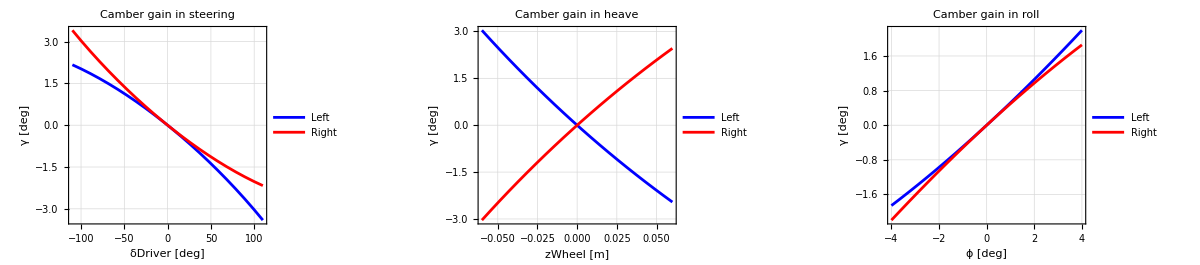

```mathematica
p1=ListPlot[{obtainedMotionSl,obtainedMotionSr},Joined->True,PlotStyle->{Blue,Red},PlotLabel->Style["Camber gain in steering",FontSize->18],
Frame->True,FrameLabel->{"δDriver [deg]","γ [deg]"},GridLines->Automatic,ImageSize->400,PlotLegends->Placed[{"Left","Right"},{Right,Top}]];
p2=ListPlot[{obtainedMotionZl,obtainedMotionZr},Joined->True,PlotStyle->{Blue,Red},PlotLabel->Style["Camber gain in heave",FontSize->18],Frame->True,FrameLabel->{"zWheel [m]","γ [deg]"},GridLines->Automatic,ImageSize->400,PlotLegends->Placed[{"Left","Right"},{Right,Top}]];
p3=ListPlot[{obtainedMotionϕl,obtainedMotionϕr},Joined->True,PlotStyle->{Blue,Red},PlotLabel->Style["Camber gain in roll",FontSize->18],Frame->True,FrameLabel->{"ϕ [deg]","γ [deg]"},GridLines->Automatic,ImageSize->400,PlotLegends->Placed[{"Left","Right"},{Right,Top}]];
GraphicsRow[{p1,p2,p3},Frame->All,AspectRatio->1/3,ImageSize->1200,Alignment->Left]
```

#### Kingpin gain

```mathematica
obtainedMotionSl=ConstantArray[{0,0},nsteps+1];(*steering*)
obtainedMotionSr=ConstantArray[{0,0},nsteps+1];(*steering*)
obtainedMotionZl=ConstantArray[{0,0},nsteps+1];(*bump*)
obtainedMotionZr=ConstantArray[{0,0},nsteps+1];(*bump*)
obtainedMotionϕl=ConstantArray[{0,0},nsteps+1];(*roll*)
obtainedMotionϕr=ConstantArray[{0,0},nsteps+1];(*roll*)
For[i=1,i<=nsteps+1,i++,
(*kingpin in steering*)
eqnsS=Phi/.dofSeqS[[i]]/.setup/.dataKine;
solS=FindRoot[eqnsS,guess];
obtainedMotionSl[[i,1]]=dofSeqS[[i,2,2]]*180/π;
obtainedMotionSr[[i,1]]=dofSeqS[[i,2,2]]*180/π;
obtainedMotionSl[[i,2]]=ArcTan[((P7l[[2]]-P6l[[2]])/(P6l[[3]]-P7l[[3]]))/.solS/.dofSeqS[[i]]/.setup/.dataKine]*180/π;
obtainedMotionSr[[i,2]]=ArcTan[((P7r[[2]]-P6r[[2]])/(P6r[[3]]-P7r[[3]]))/.solS/.dofSeqS[[i]]/.setup/.dataKine]*180/π;
(*kingpin in bump*)
eqnsZ=Phi/.dofSeqZ[[i]]/.setup/.dataKine;
solZ=FindRoot[eqnsZ,guess];
obtainedMotionZl[[i,1]]=dofSeqZ[[i,1,2]];
obtainedMotionZr[[i,1]]=dofSeqZ[[i,1,2]];
obtainedMotionZl[[i,2]]=ArcTan[((P7l[[2]]-P6l[[2]])/(P6l[[3]]-P7l[[3]]))/.solZ/.dofSeqZ[[i]]/.setup/.dataKine]*180/π;
obtainedMotionZr[[i,2]]=ArcTan[((P7r[[2]]-P6r[[2]])/(P6r[[3]]-P7r[[3]]))/.solZ/.dofSeqZ[[i]]/.setup/.dataKine]*180/π;
(*kingpin in roll*)
eqnsϕ=Phi/.dofSeqϕ[[i]]/.setup/.dataKine;
solϕ=FindRoot[eqnsϕ,guess];
obtainedMotionϕl[[i,1]]=dofSeqϕ[[i,3,2]]*180/π;
obtainedMotionϕr[[i,1]]=dofSeqϕ[[i,3,2]]*180/π;
obtainedMotionϕl[[i,2]]=ArcTan[((P7l[[2]]-P6l[[2]])/(P6l[[3]]-P7l[[3]]))/.solϕ/.dofSeqϕ[[i]]/.setup/.dataKine]*180/π;
obtainedMotionϕr[[i,2]]=ArcTan[((P7r[[2]]-P6r[[2]])/(P6r[[3]]-P7r[[3]]))/.solϕ/.dofSeqϕ[[i]]/.setup/.dataKine]*180/π;
]
```

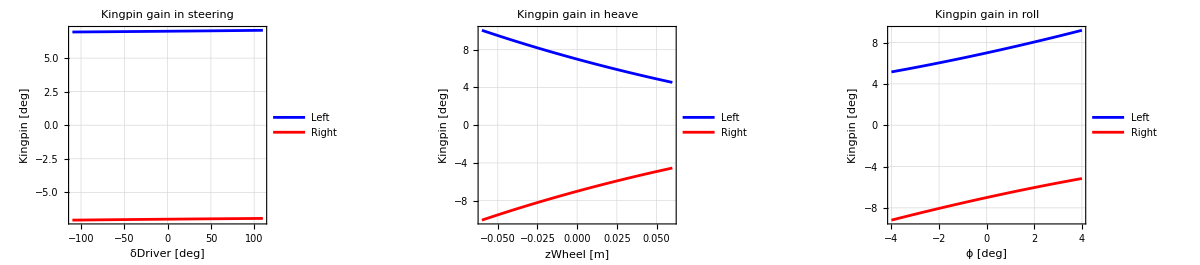

```mathematica
p1=ListPlot[{obtainedMotionSl,obtainedMotionSr},Joined->True,PlotStyle->{Blue,Red},PlotLabel->Style["Kingpin gain in steering",FontSize->18],
Frame->True,FrameLabel->{"δDriver [deg]","Kingpin [deg]"},GridLines->Automatic,ImageSize->400,PlotLegends->Placed[{"Left","Right"},{Right,Top}]];
p2=ListPlot[{obtainedMotionZl,obtainedMotionZr},Joined->True,PlotStyle->{Blue,Red},PlotLabel->Style["Kingpin gain in heave",FontSize->18],Frame->True,FrameLabel->{"zWheel [m]","Kingpin [deg]"},GridLines->Automatic,ImageSize->400,PlotLegends->Placed[{"Left","Right"},{Right,Top}]];
p3=ListPlot[{obtainedMotionϕl,obtainedMotionϕr},Joined->True,PlotStyle->{Blue,Red},PlotLabel->Style["Kingpin gain in roll",FontSize->18],Frame->True,FrameLabel->{"ϕ [deg]","Kingpin [deg]"},GridLines->Automatic,ImageSize->400,PlotLegends->Placed[{"Left","Right"},{Right,Top}]];
GraphicsRow[{p1,p2,p3},Frame->All,AspectRatio->1/3,ImageSize->1200,Alignment->Left]
```

#### Caster gain

```mathematica
obtainedMotionSl=ConstantArray[{0,0},nsteps+1];(*steering*)
obtainedMotionSr=ConstantArray[{0,0},nsteps+1];(*steering*)
obtainedMotionZl=ConstantArray[{0,0},nsteps+1];(*bump*)
obtainedMotionZr=ConstantArray[{0,0},nsteps+1];(*bump*)
obtainedMotionϕl=ConstantArray[{0,0},nsteps+1];(*roll*)
obtainedMotionϕr=ConstantArray[{0,0},nsteps+1];(*roll*)
For[i=1,i<=nsteps+1,i++,
(*caster in steering*)
eqnsS=Phi/.dofSeqS[[i]]/.setup/.dataKine;
solS=FindRoot[eqnsS,guess];
obtainedMotionSl[[i,1]]=dofSeqS[[i,2,2]]*180/π;
obtainedMotionSr[[i,1]]=dofSeqS[[i,2,2]]*180/π;
obtainedMotionSl[[i,2]]=ArcTan[((P7l[[1]]-P6l[[1]])/(P6l[[3]]-P7l[[3]]))/.solS/.dofSeqS[[i]]/.setup/.dataKine]*180/π;
obtainedMotionSr[[i,2]]=ArcTan[((P7r[[1]]-P6r[[1]])/(P6r[[3]]-P7r[[3]]))/.solS/.dofSeqS[[i]]/.setup/.dataKine]*180/π;
(*caster in bump*)
eqnsZ=Phi/.dofSeqZ[[i]]/.setup/.dataKine;
solZ=FindRoot[eqnsZ,guess];
obtainedMotionZl[[i,1]]=dofSeqZ[[i,1,2]];
obtainedMotionZr[[i,1]]=dofSeqZ[[i,1,2]];
obtainedMotionZl[[i,2]]=ArcTan[((P7l[[1]]-P6l[[1]])/(P6l[[3]]-P7l[[3]]))/.solZ/.dofSeqZ[[i]]/.setup/.dataKine]*180/π;
obtainedMotionZr[[i,2]]=ArcTan[((P7r[[1]]-P6r[[1]])/(P6r[[3]]-P7r[[3]]))/.solZ/.dofSeqZ[[i]]/.setup/.dataKine]*180/π;
(*caster in roll*)
eqnsϕ=Phi/.dofSeqϕ[[i]]/.setup/.dataKine;
solϕ=FindRoot[eqnsϕ,guess];
obtainedMotionϕl[[i,1]]=dofSeqϕ[[i,3,2]]*180/π;
obtainedMotionϕr[[i,1]]=dofSeqϕ[[i,3,2]]*180/π;
obtainedMotionϕl[[i,2]]=ArcTan[((P7l[[1]]-P6l[[1]])/(P6l[[3]]-P7l[[3]]))/.solϕ/.dofSeqϕ[[i]]/.setup/.dataKine]*180/π;
obtainedMotionϕr[[i,2]]=ArcTan[((P7r[[1]]-P6r[[1]])/(P6r[[3]]-P7r[[3]]))/.solϕ/.dofSeqϕ[[i]]/.setup/.dataKine]*180/π;
]
```

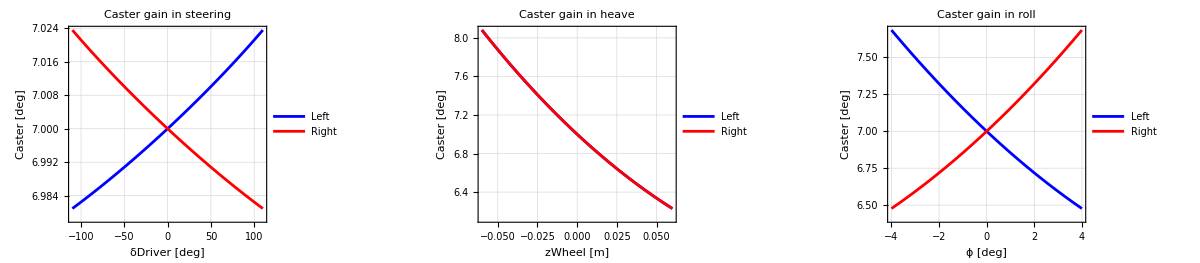

```mathematica
p1=ListPlot[{obtainedMotionSl,obtainedMotionSr},Joined->True,PlotStyle->{Blue,Red},PlotLabel->Style["Caster gain in steering",FontSize->18],
Frame->True,FrameLabel->{"δDriver [deg]","Caster [deg]"},GridLines->Automatic,ImageSize->400,PlotLegends->Placed[{"Left","Right"},{Right,Top}]];
p2=ListPlot[{obtainedMotionZl,obtainedMotionZr},Joined->True,PlotStyle->{Blue,Red},PlotLabel->Style["Caster gain in heave",FontSize->18],Frame->True,FrameLabel->{"zWheel [m]","Caster [deg]"},GridLines->Automatic,ImageSize->400,PlotLegends->Placed[{"Left","Right"},{Right,Top}]];
p3=ListPlot[{obtainedMotionϕl,obtainedMotionϕr},Joined->True,PlotStyle->{Blue,Red},PlotLabel->Style["Caster gain in roll",FontSize->18],Frame->True,FrameLabel->{"ϕ [deg]","Caster [deg]"},GridLines->Automatic,ImageSize->400,PlotLegends->Placed[{"Left","Right"},{Right,Top}]];
GraphicsRow[{p1,p2,p3},Frame->All,AspectRatio->1/3,ImageSize->1200,Alignment->Left]
```

#### RCH

```mathematica
obtainedMotionS=ConstantArray[{0,0},nsteps+1];(*steering*)
obtainedMotionZ=ConstantArray[{0,0},nsteps+1];(*bump*)
obtainedMotionϕ=ConstantArray[{0,0},nsteps+1];(*roll*)
For[i=1,i<=nsteps+1,i++,
(*caster in steering*)
eqnsS=Phi/.dofSeqS[[i]]/.setup/.dataKine;
solS=FindRoot[eqnsS,guess];
subs=Flatten[{solS,dofSeqS[[i]],setup,dataKine}];
ICRwl=intersection[P12l/.subs,{P7l[[2]],P7l[[3]]}/.subs,P34l/.subs,{P6l[[2]],P6l[[3]]}/.subs];
ICRwr=intersection[P12r/.subs,{P7r[[2]],P7r[[3]]}/.subs,P34r/.subs,{P6r[[2]],P6r[[3]]}/.subs];
ICRchassis=intersection[ICRwl,PClval/.subs,ICRwr,PCrval/.subs];
obtainedMotionS[[i,1]]=dofSeqS[[i,2,2]]*180/π;
obtainedMotionS[[i,2]]=ICRchassis[[2]];
(*caster in bump*)
eqnsZ=Phi/.dofSeqZ[[i]]/.setup/.dataKine;
solZ=FindRoot[eqnsZ,guess];
subs=Flatten[{solZ,dofSeqZ[[i]],setup,dataKine}];
ICRwl=intersection[P12l/.subs,{P7l[[2]],P7l[[3]]}/.subs,P34l/.subs,{P6l[[2]],P6l[[3]]}/.subs];
ICRwr=intersection[P12r/.subs,{P7r[[2]],P7r[[3]]}/.subs,P34r/.subs,{P6r[[2]],P6r[[3]]}/.subs];
ICRchassis=intersection[ICRwl,PClval/.subs,ICRwr,PCrval/.subs];
obtainedMotionZ[[i,1]]=dofSeqZ[[i,1,2]];
obtainedMotionZ[[i,2]]=ICRchassis[[2]];
(*caster in roll*)
eqnsϕ=Phi/.dofSeqϕ[[i]]/.setup/.dataKine;
solϕ=FindRoot[eqnsϕ,guess];
subs=Flatten[{solϕ,dofSeqϕ[[i]],setup,dataKine}];
ICRwl=intersection[P12l/.subs,{P7l[[2]],P7l[[3]]}/.subs,P34l/.subs,{P6l[[2]],P6l[[3]]}/.subs];
ICRwr=intersection[P12r/.subs,{P7r[[2]],P7r[[3]]}/.subs,P34r/.subs,{P6r[[2]],P6r[[3]]}/.subs];
ICRchassis=intersection[ICRwl,PClval/.subs,ICRwr,PCrval/.subs];
obtainedMotionϕ[[i,1]]=dofSeqϕ[[i,3,2]]*180/π;
obtainedMotionϕ[[i,2]]=ICRchassis[[2]];
]
```

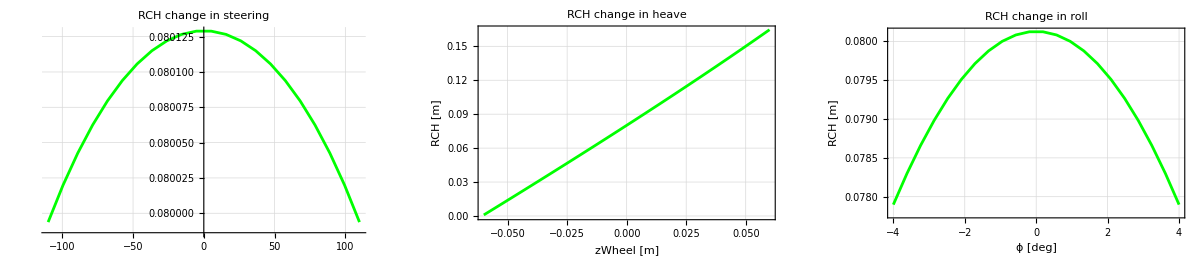

```mathematica
p1=ListPlot[obtainedMotionS,Joined->True,PlotStyle->Green,PlotLabel->Style["RCH change in steering",FontSize->18],
Frame->True§,FrameLabel->{"δDriver [deg]","RCH [m]"},GridLines->Automatic,ImageSize->400];
p2=ListPlot[obtainedMotionZ,Joined->True,PlotStyle->Green,PlotLabel->Style["RCH change in heave",FontSize->18],Frame->True,FrameLabel->{"zWheel [m]","RCH [m]"},GridLines->Automatic,ImageSize->400];
p3=ListPlot[obtainedMotionϕ,Joined->True,PlotStyle->Green,PlotLabel->Style["RCH change in roll",FontSize->18],Frame->True,FrameLabel->{"ϕ [deg]","RCH [m]"},GridLines->Automatic,ImageSize->400];
GraphicsRow[{p1,p2,p3},Frame->All,AspectRatio->1/3,ImageSize->1200,Alignment->Left]
```

#### RC y change

```mathematica
obtainedMotionS=ConstantArray[{0,0},nsteps+1];(*steering*)
obtainedMotionZ=ConstantArray[{0,0},nsteps+1];(*bump*)
obtainedMotionϕ=ConstantArray[{0,0},nsteps+1];(*roll*)
For[i=1,i<=nsteps+1,i++,
(*caster in steering*)
eqnsS=Phi/.dofSeqS[[i]]/.setup/.dataKine;
solS=FindRoot[eqnsS,guess];
subs=Flatten[{solS,dofSeqS[[i]],setup,dataKine}];
ICRwl=intersection[P12l/.subs,{P7l[[2]],P7l[[3]]}/.subs,P34l/.subs,{P6l[[2]],P6l[[3]]}/.subs];
ICRwr=intersection[P12r/.subs,{P7r[[2]],P7r[[3]]}/.subs,P34r/.subs,{P6r[[2]],P6r[[3]]}/.subs];
ICRchassis=intersection[ICRwl,PClval/.subs,ICRwr,PCrval/.subs];
obtainedMotionS[[i,1]]=dofSeqS[[i,2,2]]*180/π;
obtainedMotionS[[i,2]]=ICRchassis[[1]];
(*caster in bump*)
eqnsZ=Phi/.dofSeqZ[[i]]/.setup/.dataKine;
solZ=FindRoot[eqnsZ,guess];
subs=Flatten[{solZ,dofSeqZ[[i]],setup,dataKine}];
ICRwl=intersection[P12l/.subs,{P7l[[2]],P7l[[3]]}/.subs,P34l/.subs,{P6l[[2]],P6l[[3]]}/.subs];
ICRwr=intersection[P12r/.subs,{P7r[[2]],P7r[[3]]}/.subs,P34r/.subs,{P6r[[2]],P6r[[3]]}/.subs];
ICRchassis=intersection[ICRwl,PClval/.subs,ICRwr,PCrval/.subs];
obtainedMotionZ[[i,1]]=dofSeqZ[[i,1,2]];
obtainedMotionZ[[i,2]]=ICRchassis[[1]];
(*caster in roll*)
eqnsϕ=Phi/.dofSeqϕ[[i]]/.setup/.dataKine;
solϕ=FindRoot[eqnsϕ,guess];
subs=Flatten[{solϕ,dofSeqϕ[[i]],setup,dataKine}];
ICRwl=intersection[P12l/.subs,{P7l[[2]],P7l[[3]]}/.subs,P34l/.subs,{P6l[[2]],P6l[[3]]}/.subs];
ICRwr=intersection[P12r/.subs,{P7r[[2]],P7r[[3]]}/.subs,P34r/.subs,{P6r[[2]],P6r[[3]]}/.subs];
ICRchassis=intersection[ICRwl,PClval/.subs,ICRwr,PCrval/.subs];
obtainedMotionϕ[[i,1]]=dofSeqϕ[[i,3,2]]*180/π;
obtainedMotionϕ[[i,2]]=ICRchassis[[1]];
]
```

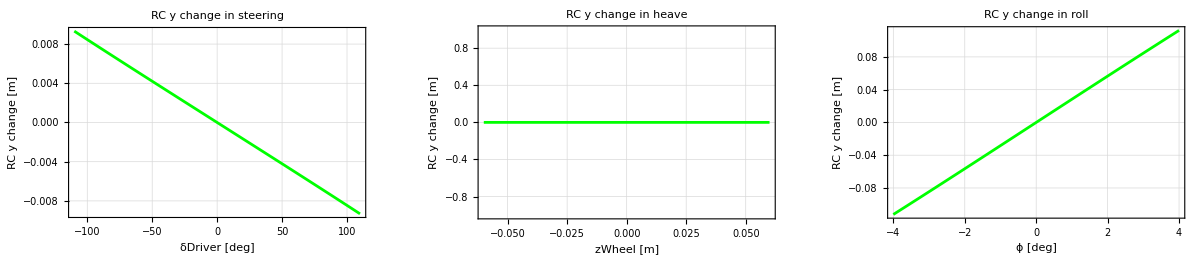

```mathematica
p1=ListPlot[obtainedMotionS,Joined->True,PlotStyle->Green,PlotLabel->Style["RC y change in steering",FontSize->18],
Frame->True,FrameLabel->{"δDriver [deg]","RC y change [m]"},GridLines->Automatic,ImageSize->400];
p2=ListPlot[obtainedMotionZ,Joined->True,PlotStyle->Green,PlotLabel->Style["RC y change in heave",FontSize->18],Frame->True,FrameLabel->{"zWheel [m]","RC y change [m]"},GridLines->Automatic,ImageSize->400];
p3=ListPlot[obtainedMotionϕ,Joined->True,PlotStyle->Green,PlotLabel->Style["RC y change in roll",FontSize->18],Frame->True,FrameLabel->{"ϕ [deg]","RC y change [m]"},GridLines->Automatic,ImageSize->400];
GraphicsRow[{p1,p2,p3},Frame->All,AspectRatio->1/3,ImageSize->1200,Alignment->Left]
```

## Maps

```mathematica
evalTable=Table[{ΔZ[t]->ΔZmin+(ΔZmax-ΔZmin)/nsteps*i,δDriver[t]->δmin+(δmax-δmin)/nsteps*j,ϕ[t]->0},{i,0,nsteps},{j,0,nsteps}];
```

```mathematica
(*Logging x9, y9, z9, Δz, δDriver*)
obtainedMotion=ConstantArray[{0,0,0,0,0},{nsteps+1,nsteps+1}];
For[i=1,i<=nsteps+1,i++,
For[j=1,j<=nsteps+1,j++,
eqns=Phi/.evalTable[[i,j]]/.setup/.dataKine;
sol=FindRoot[eqns,guess];
obtainedMotion[[i,j,1]]=sol[[1,2]];(*xWl*)
obtainedMotion[[i,j,2]]=sol[[3,2]];(*yWl*)
obtainedMotion[[i,j,3]]=sol[[5,2]];(*zWl*)
obtainedMotion[[i,j,4]]=evalTable[[i,j,1,2]];(*Δz*)
obtainedMotion[[i,j,5]]=evalTable[[i,j,2,2]];(*δDriver*)
]]
```

```mathematica
ListPointPlot3D[obtainedMotion[[All,All,{4,5,1}]],PlotStyle->Red,PlotRange->All,AxesLabel->{"Δz","δDriver","xWl"},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[obtainedMotion[[All,All,{4,5,2}]],PlotStyle->Green,PlotRange->All,AxesLabel->{"Δz","δDriver","yWl"},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[obtainedMotion[[All,All,{4,5,3}]],PlotStyle->Green,PlotRange->All,AxesLabel->{"Δz","δDriver","zWl"},BoxRatios->{1,1,1}]
```

-Graphics3D-